```mathematica
(*here iare the equations and set parameters, as well as the potential*)
V[x_]:=-0.5 x^2+0.25 β x^4;
hbar=1;
β=0.01;
Γ=.1;
ω=Pi/3;
ϕ=0;
g=0.3;
(*these are the differential equations we must solve*)
eqns={x'[t]==p[t],
p'[t]==(g Cos[t ω])/β-2 Γ p[t]+x[t]-β^2 x[t]^3-3 β^2 x[t] χ[t]^2,
χ'[t]==Π[t]+1/2 Γ (Sin[ϕ]^2/χ[t]+4 Cos[ϕ]^2 χ[t]-4 Sin[ϕ]^2 Π[t]^2 χ[t]-4 Cos[ϕ]^2 χ[t]^3-2 Sin[2 ϕ] Π[t] (-1+2 χ[t]^2)),
Π'[t]==1/(4 χ[t]^3)(1+Γ Sin[2 ϕ]-8 Γ Sin[ϕ]^2 Π[t]^3 χ[t]^3-8 Γ Sin[2 ϕ] Π[t]^2 χ[t]^4+4 Γ Sin[2 ϕ] χ[t]^2 (-1+χ[t]^2)-2 Γ Π[t] χ[t] (3 Sin[ϕ]^2+4 Cos[ϕ]^2 χ[t]^2 (1+χ[t]^2))-4 χ[t]^4 (-1+3 β^2 (x[t]^2+χ[t]^2))),
sr'[t]== 1/χ[t]^2(-0.25-0.25 Γ Cos[ϕ] Sin[ϕ]+χ[t] (1. Γ Cos[ϕ] Sin[ϕ] Π[t]^2 χ[t]+Γ Π[t] (0.5-0.5 Cos[2 ϕ]+(1.+1. Cos[2 ϕ]) χ[t]^2)+χ[t] (0.5 p[t]^2+0.5 x[t]^2-1. β^2 x[t]^4+1.5 β^2 χ[t]^4+Γ Cos[ϕ] Sin[ϕ] (1.-1. χ[t]^2)))),
si'[t]==I Log[χ[t]],x[0]==5, p[0]==1,Π[0]==0.99,χ[0]==0.4,sr[0]==0.2 ,si[0]==1};
(*we solve*)
sol=NDSolve[eqns,{x[t],p[t],Π[t],χ[t],sr[t],si[t]},{t,0,100}]
```

{{x[t]→InterpolatingFunction[…][t],p[t]→InterpolatingFunction[…][t],Π[t]→InterpolatingFunction[…][t],χ[t]→InterpolatingFunction[…][t],sr[t]→InterpolatingFunction[…][t],si[t]→InterpolatingFunction[…][t]}}

```mathematica
(*Here are the plots of each variable vs time -- note we plot s as Real and Imaginary*)
```

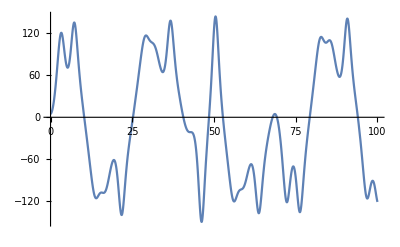

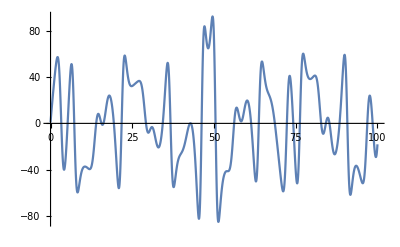

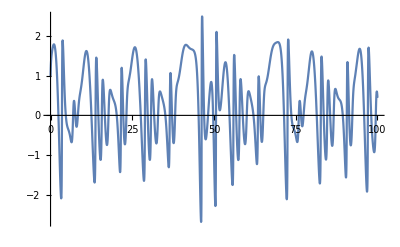

```mathematica
Plot[x[t]/.sol,{t,0,100}, PlotRange->Full]
Plot[p[t]/.sol,{t,0,100}, PlotRange->Full]
(*ParametricPlot[{p[t]/.sol,x[t]/.sol},{t,0,20},PlotRange->Full]*)
Plot[Π[t]/.sol,{t,0,100}]
```

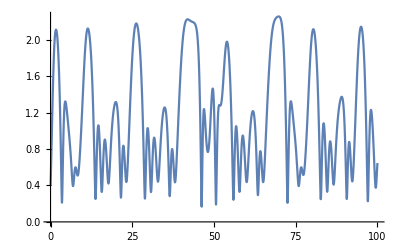

```mathematica
Plot[χ[t]/.sol,{t,0,100}]
```

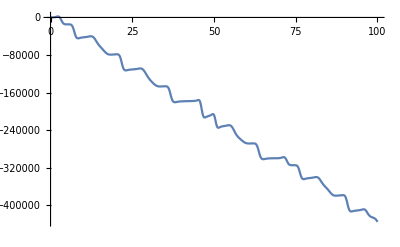

```mathematica
Plot[sr[t]/.sol,{t,0,100}]
```

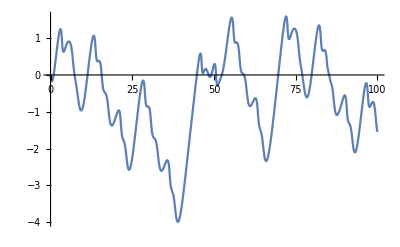

```mathematica
Plot[Im[si[t]/.sol],{t,0,100}]
```

```mathematica
(*initial conditions again and we have the function solutions reorganized into new variables so we don have to right /.sol forever*)
x0=5;
p0=1;
Π0=0.99;
χ0=0.4;
s0=0.2;
x1[t_]:=x[t]/.sol;
p1[t_]:=p[t]/.sol;
Π1[t_]:=Π[t]/.sol;
χ1[t_]:=χ[t]/.sol;
s1[t_]:=s[t]/.sol;
(*here is psi & psiStar as before*)
psi[q_,t_]:=Exp[(I/hbar)((q-x1[t])(Π1[t]/(2 hbar χ1[t])+I hbar /((4χ1[t])^2))(q-x1[t])+p1[t](q-x1[t])+s1[t])]; 
psistar[q_]:=Exp[(-I/hbar)((q-x0)(Π0/(2 hbar χ0)+I hbar /(4χ0^2))(q-x0)+p0(q-x0)+s0)];
```

```mathematica
(*We can plot the integrand between a certain time at a fixed q*)
(*Plot[Re[psistar[q]psi[q,t]],{t,0,1}]*)
```

```mathematica
(*and integrate it*)
NIntegrate[psistar[q]psi[q,t],{q,-Infinity,Infinity}]
```

NIntegrate::inumr: The integrand ⅇ^(-ⅈ (-4.8+(1.2375+1.5625 ⅈ) (-5+q)^2+q)+ⅈ (s[t]+«21»[«1»][t] (q-«1»)+(1/16 ⅈ Power[«2»]+1/2 Power[«2»] InterpolatingFunction[«5»][«1»]) (q+Times[«1»])^2)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞,0.}}.

{NIntegrate[ⅇ^(-ⅈ (-4.8+(1.2375+1.5625 ⅈ) (-5+q)^2+q)+ⅈ (s[t]+InterpolatingFunction[…][t] (q-InterpolatingFunction[…][t])+(ⅈ/(16 (InterpolatingFunction[…][t])^2)+(InterpolatingFunction[…][t])/(2 InterpolatingFunction[…][t])) (q-InterpolatingFunction[…][t])^2)),{q,-∞,∞}]}

```mathematica
(*and here is what happens if we integrate over all of q*)
```

```mathematica
NIntegrate[psistar[q]psi[q,t],{q,0,1},{t,0.1,10}]
```

{1.52907×10^13+6.99117×10^12 ⅈ}

```mathematica
(*bad...*)
```

```mathematica
Clear[hbar,β,Γ,ω,ϕ,g,t]
```

```mathematica
FullSimplify[p[t]^2+0.5(Π[t](Π[t] +Γ*((χ[t]-χ[t]^3+χ[t] Π[t]^2-1/(4 χ[t]))Cos[2*ϕ]-Π[t](-1+2 χ[t]^2) Sin[2*ϕ]+χ[t]-χ[t]^3-χ[t] Π[t]^2+1/(4 χ[t])))- χ[t](χ[t] (1-3 β^2 (x[t]^2+χ[t]^2))+1/(4 χ[t]^3)+Γ ((Π[t]^3-Π[t]+3 Π[t]/(4 χ[t]^2)-Π[t] χ[t]^2) Cos[2 ϕ]-(-1/(4 χ[t]^3)+1/χ[t]-χ[t]+2 χ[t] Π[t]^2) Sin[2 ϕ]+(-Π[t]^3-Π[t]-3 Π[t]/(4 χ[t]^2)-Π[t] χ[t]^2))))-0.5p[t]^2-0.5Π[t]^2+0.5 x[t]^2-0.25 β ^2x[t]^4-0.75 β^2 x[t]^4+0.5χ[t]^2-1/(8χ[t]^2)-1.5 β^2  x[t]^2 χ[t]^2]
```

1/χ[t]^2(-0.25-0.25 Γ Cos[ϕ] Sin[ϕ]+χ[t] (1. Γ Cos[ϕ] Sin[ϕ] Π[t]^2 χ[t]+Γ Π[t] (0.5-0.5 Cos[2 ϕ]+(1.+1. Cos[2 ϕ]) χ[t]^2)+χ[t] (0.5 p[t]^2+0.5 x[t]^2-1. β^2 x[t]^4+1.5 β^2 χ[t]^4+Γ Cos[ϕ] Sin[ϕ] (1.-1. χ[t]^2))))